# Saturation Demonstrations

## Waveshaping

We solve boundary conditions to find a third-order polynomial waveshaping function

```mathematica
f[x_] := a x^3 + b x^2 + c x +d
fp[x_] := 3a x^2 + 2b x + c
Solve[f[-1]==-1&&f[1]==1&&f'[-1]==0&&f'[1]==0,{a,b,c,d}]
```

{{a→-1/2,b→0,c→3/2,d→0}}

```mathematica
ws[x_]:=-1/2 Clip[x] (-3+Clip[x]^2)
```

Identity function plot (left) compared to third-order waveshaping function plot (right)

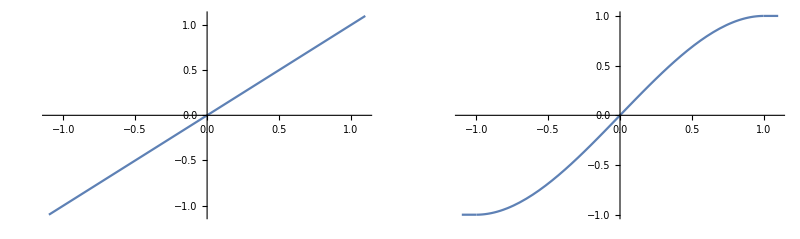

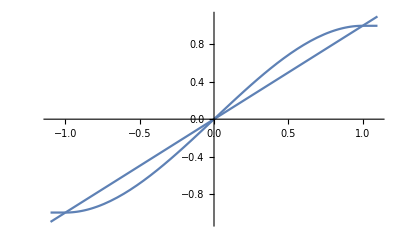

```mathematica
GraphicsRow[{
Plot[x,{x,-1.1,1.1}],
Plot[ws[x],{x,-1.1,1.1}]
}, ImageSize->Full]
Show[
Plot[x,{x,-1.1,1.1}],
Plot[ws[x],{x,-1.1,1.1}]
, ImageSize->Full]
```

Sine wave input (left) and waveshaped sine wave (right)

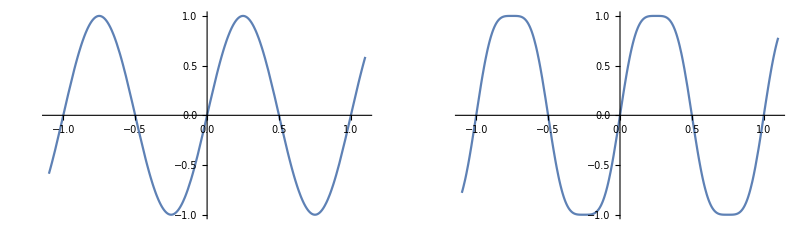

```mathematica
GraphicsRow[{
Plot[Sin[2π x],{x,-1.1,1.1}],
Plot[ws[Sin[2π x]],{x,-1.1,1.1}]
}, ImageSize->Full]
```

Third order polynomial waveshaped sine wave (left) and Tanh function waveshaping (right)

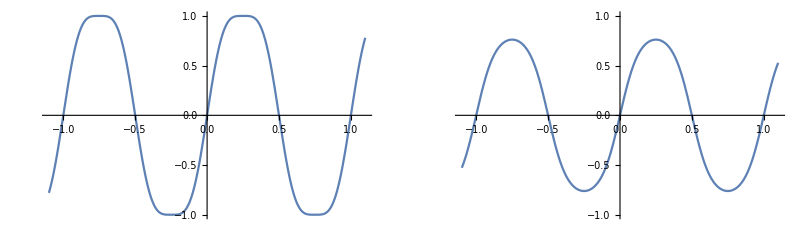

```mathematica
GraphicsRow[{
Plot[ws[Sin[2π x]],{x,-1.1,1.1},PlotRange->{-1,1}],
Plot[Tanh[Sin[2π x]],{x,-1.1,1.1},PlotRange->{-1,1}]
}, ImageSize->Full]
```

Demonstration of the effect of waveshaping in response to gain boosted signals

```mathematica
dbToGain[gain_]:=10^(gain/20)
Manipulate[Plot[Tanh[dbToGain[gainDb]Sin[2π x]],{x,-1.1,1.1},PlotRange->{-1,1},ImageSize->Large],
{gainDb,-6,40}]
```

## How much is 100 dB of gain?

```mathematica
Style[Table[{g,dbToGain[N[g]]},{g,0,100,20}]//TableForm,FontSize->36]
```

0 | 1.
20 | 10.
40 | 100.
60 | 1000.
80 | 10000.
100 | 100000.

## Sine-sweep generation code

```mathematica
LogarithmicSineSweep[startFreq_,endFreq_,lengthSeconds_,sampleRate_]:=Module[{output,lengthSamples,i,phase=0,phaseIncrement,frequency},lengthSamples=N[lengthSeconds*sampleRate];
output=Table[0,{t,1,lengthSamples}];
For[i=1,i≤lengthSamples,i++,output[[i]]=Sin[N[phase]];
frequency=2^(Log2[startFreq]+Log2[endFreq/startFreq](i/lengthSamples));
phaseIncrement=2 π frequency/sampleRate;
phase+=phaseIncrement;
If[phase > 2π,phase -= 2π];
];
output]

(* six second sine sweep *)
sampleRate = 48000;
sineSweep = LogarithmicSineSweep[20,sampleRate/2,6,sampleRate];
```

## Spectrograms of original sine sweep (1), polynomial waveshaped sweep (2), and tanh waveshaped sweep (3)

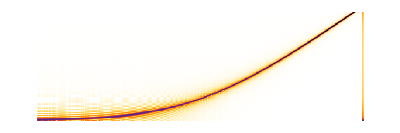

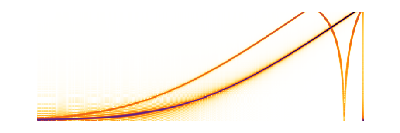

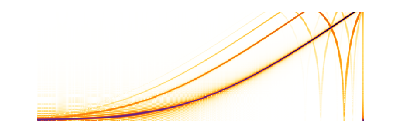

```mathematica
Spectrogram[sineSweep,2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
Spectrogram[ws/@sineSweep,2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
Spectrogram[Tanh/@sineSweep,2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
```

## How does a gain boost affect aliasing?

Ten decibels

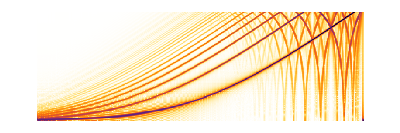

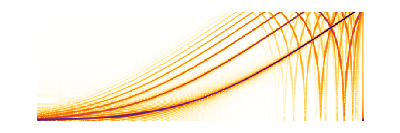

```mathematica
Spectrogram[ws/@(dbToGain[10]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
Spectrogram[Tanh/@(dbToGain[10]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
```

Twenty decibels

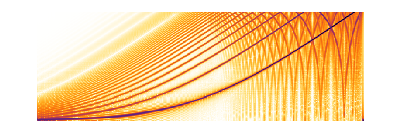

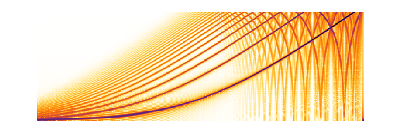

```mathematica
Spectrogram[ws/@(dbToGain[20]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
Spectrogram[Tanh/@(dbToGain[20]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
```

Fourty decibels

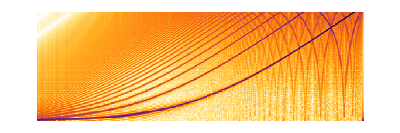

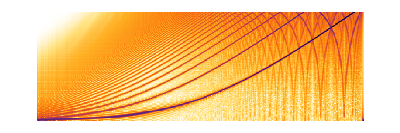

```mathematica
Spectrogram[ws/@(dbToGain[40]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
Spectrogram[Tanh/@(dbToGain[40]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
```

One Hundred decibels

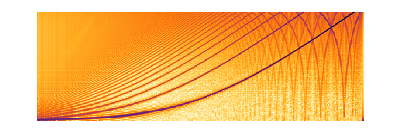

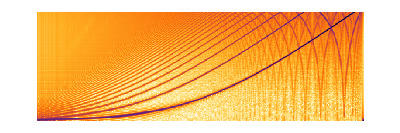

```mathematica
Spectrogram[ws/@(dbToGain[100]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
Spectrogram[Tanh/@(dbToGain[100]sineSweep),2048,Method->{"MelFrequency",200,20,20000},SampleRate->48000,PlotRange->All,ImageSize->Full]
```

## Does it get cleaner if we oversample?

```mathematica
(* six second sine sweep *)
oversamplingFactor = 8;
sampleRate = 48000 oversamplingFactor;
sineSweep8 = ArrayResample[sineSweep,oversamplingFactor Length[sineSweep]];

(* One Hundred decibels *)
Spectrogram[ws/@(dbToGain[100]sineSweep8),2048*oversamplingFactor,Method->{"MelFrequency",200,20,20000},SampleRate->sampleRate,PlotRange->All,ImageSize->Full]
Spectrogram[Tanh/@(dbToGain[100]sineSweep8),2048*oversamplingFactor,Method->{"MelFrequency",200,20,20000},SampleRate->sampleRate,PlotRange->All,ImageSize->Full]
```

-Graphics-

-Graphics-

```mathematica
(* six second sine sweep *)
oversamplingFactor = 64;
sampleRate = 48000 oversamplingFactor;
sineSweep64 = ArrayResample[sineSweep,oversamplingFactor Length[sineSweep]];

(* One Hundred decibels *)
Spectrogram[ws/@(dbToGain[100]sineSweep64),2048*oversamplingFactor,Method->{"MelFrequency",200,20,20000},SampleRate->sampleRate,PlotRange->All,ImageSize->Full]
Spectrogram[Tanh/@(dbToGain[100]sineSweep64),2048*oversamplingFactor,Method->{"MelFrequency",200,20,20000},SampleRate->sampleRate,PlotRange->All,ImageSize->Full]
```

-Graphics-

-Graphics-